```mathematica
ResourceFunction["InterpolatingFunctionDomain"]
```

[◼] | InterpolatingFunctionDomain

```mathematica
rootDir=ParentDirectory[NotebookDirectory[],2]
```

/home/daniel/Research/ActionMinimization

## Importing PES and inertia

```mathematica
MassParams=Import[rootDir<>"/PES/mass2030.out"];
```

```mathematica
b22=Transpose@Join[Transpose@MassParams[[2;;,1;;3]],{MassParams[[2;;,4]]}];
b33=Transpose@Join[Transpose@MassParams[[2;;,1;;3]],{MassParams[[2;;,5]]}];
bll=Transpose@Join[Transpose@MassParams[[2;;,1;;3]],{MassParams[[2;;,6]]}];
b23=Transpose@Join[Transpose@MassParams[[2;;,1;;3]],{MassParams[[2;;,7]]}];
b2l=Transpose@Join[Transpose@MassParams[[2;;,1;;3]],{MassParams[[2;;,8]]}];
b3l=Transpose@Join[Transpose@MassParams[[2;;,1;;3]],{MassParams[[2;;,9]]}];
```

```mathematica
listOfMasses={b22,b33,bll,b23,b2l,b3l};
```

```mathematica
interpMassTable=Table[Interpolation[listOfMasses[[i]],InterpolationOrder->3],{i,1,6}];
```

```mathematica
PotentialVals=Import[rootDir<>"/PES/pot2030.out","Table",HeaderLines->2];
```

```mathematica
pes=Transpose@Join[Transpose@PotentialVals[[;;,1;;3]],{PotentialVals[[;;,4]]}];
```

```mathematica
interpPes=Interpolation[pes,InterpolationOrder->3];
```

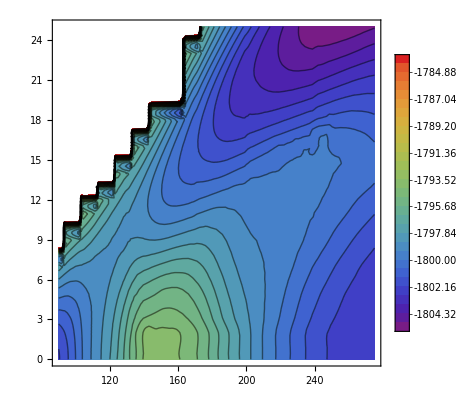

```mathematica
ContourPlot[interpPes[x,y,0],{x,90,275},{y,0,25},Contours->30,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

## Importing and interpolating paths

```mathematica
pathNames=FileNames["*.txt",rootDir<>"/Paths/240Pu"];
```

```mathematica
pathsList=Table[Import[pathNames[[i]],"CSV",Numeric->True],{i,1,Length[pathNames]}];
```

```mathematica
Table[{StringSplit[pathNames[[i]],"/"][[-1]],Dimensions[pathsList[[i]]]},{i,1,Length[pathsList]}]//MatrixForm
```

(240Pu_3D_DPM_cont_mass_path.txt | {98,3}
240Pu_3D_DPM_varied_mass_path.txt | {98,3}
dijkstra_mass.txt | {205,3}
dijkstra_no_mass.txt | {98,3}
ELE240PuConstantMass.txt | {302,2}
ELE240PuVariedMass.txt | {301,3}
Eric_240Pu_LAP_Mass_False_path.txt | {32,3}
Eric_240Pu_MEP_Mass_False_path.txt | {32,3}
Final_240Pu_LAP_Mass_True_DP_Init_path.txt | {194,3}
Final_240Pu_LAP_Mass_True_Line_Init_path.txt | {102,3})

```mathematica
For[i=1,i<=Length[pathsList],i++,
If[Dimensions[pathsList[[i]]][[2]]==2,pathsList[[i]]=Transpose@Join[Transpose@pathsList[[i]],{ConstantArray[0,Dimensions[pathsList[[i]]][[1]]]}],None]]
```

```mathematica
Table[{StringSplit[pathNames[[i]],"/"][[-1]],Dimensions[pathsList[[i]]]},{i,1,Length[pathsList]}]//MatrixForm
```

(240Pu_3D_DPM_cont_mass_path.txt | {98,3}
240Pu_3D_DPM_varied_mass_path.txt | {98,3}
dijkstra_mass.txt | {205,3}
dijkstra_no_mass.txt | {98,3}
ELE240PuConstantMass.txt | {302,3}
ELE240PuVariedMass.txt | {301,3}
Eric_240Pu_LAP_Mass_False_path.txt | {32,3}
Eric_240Pu_MEP_Mass_False_path.txt | {32,3}
Final_240Pu_LAP_Mass_True_DP_Init_path.txt | {194,3}
Final_240Pu_LAP_Mass_True_Line_Init_path.txt | {102,3})

```mathematica
paddedPaths=Table[Transpose[{N@Range[0,1,1/(Length[pathsList[[i]]]-1)],pathsList[[i]]}],{i,1,Length[pathsList]}];
paddedPaths=Drop[paddedPaths,{3,4}];
paddedPaths=Drop[paddedPaths,{-2}];
Length[paddedPaths]
```

7

```mathematica
interpPaths[t_]=Through[Table[Interpolation[paddedPaths[[i]]],{i,1,Length[paddedPaths]}][t]];
```

## Making 3D plot

```mathematica
colors={Red,Red,Orange,Orange,Blue,Black,Blue};
styles={Hold[Nothing],Dashed,Hold[Nothing],Dashed,Hold[Nothing],Hold[Nothing],Dashed};
```

```mathematica
plotStyle=Table[{colors[[i]],AbsoluteThickness[3.25],styles[[i]]},{i,1,Length[colors]}]//ReleaseHold;
```

```mathematica
contour=ContourPlot[interpPes[x,y,0],{x,90,275},{y,0,25},FrameTicks->False,Contours->30,ColorFunction->"Rainbow",PlotRangePadding->None];
```

#### To get orientation of plot hard-coded, see https://mathematica.stackexchange.com/a/135401

```mathematica
gsCont=ContourPlot3D[interpPes[x,y,z]==-1802.5,{x,86,275},{y,15,25},{z,0,25},ContourStyle->{Green,Opacity[0.5]}];
```

```mathematica
finalPlot=
Show[
{
Graphics3D[{Texture[contour],
Polygon[{{86,0,0},{275,0,0},{275,25,0},{86,25,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},
Lighting->"Neutral",ViewPoint->{1.9749934977795132,-1.945080820631945,1.9406342481102419},Boxed->False],
gsCont,
ParametricPlot3D[Evaluate@interpPaths[t],{t,0,1},PlotStyle->plotStyle]
},
BoxRatios->{1,1,1},Axes->True,PlotRange->{{86,275},{0,25},{0,20}},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{18,GrayLevel[0]}]
```

-Graphics3D-

#### A bug with exporting to vector graphics in some versions means this crashes if I export to .pdf or .eps

```mathematica
Export[NotebookDirectory[]<>"3dplot.jpg",finalPlot,ImageResolution->500]
```

/home/daniel/Research/ActionMinimization/Paper_Figures/240Pu_paths/3dplot.jpg

## TODO: 2d plot